```mathematica
Clear["Global`*"]
```

```mathematica
Ep[k_,θ_]=ArcCos[Cos[θ/2]Cos[k]];
Em[k_,θ_]=-ArcCos[Cos[θ/2]Cos[k]];
```

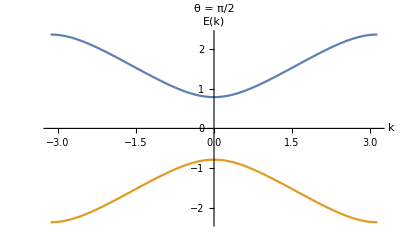

```mathematica
Plot[{Ep[k,Pi/2],Em[k,Pi/2]},{k,-Pi,Pi},AxesLabel->{k,"E(k)"},PlotLabel->"θ = π/2"]
```

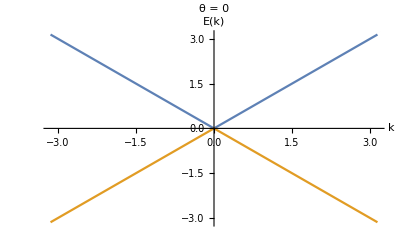

```mathematica
Plot[{Ep[k,0],Em[k,0]},{k,-Pi,Pi},AxesLabel->{k,"E(k)"},PlotLabel->"θ = 0"]
```

```mathematica
EE1[k_,θ1_,θ2_] = ArcCos[Cos[θ2/2]Cos[θ1/2]Cos[k]-Sin[θ1/2]Sin[θ2/2]];
EE2[k_,θ1_,θ2_] = -ArcCos[Cos[θ2/2]Cos[θ1/2]Cos[k]-Sin[θ1/2]Sin[θ2/2]];
```

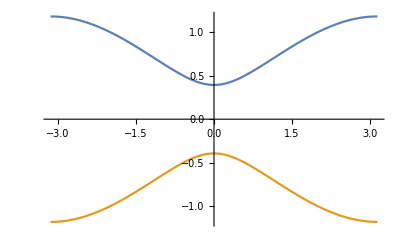

```mathematica
Plot[{EE1[k,-Pi/2,3Pi/4],EE2[k,-Pi/2,3Pi/4]},{k,-Pi,Pi}]
```

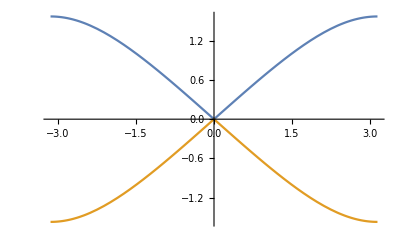

```mathematica
Plot[{EE1[k,-Pi/2,2Pi/4],EE2[k,-Pi/2,2Pi/4]},{k,-Pi,Pi}]
```

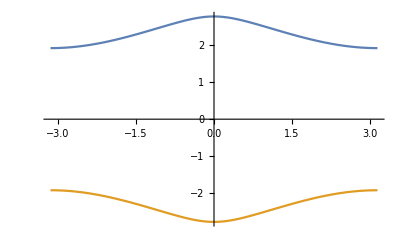

```mathematica
Plot[{EE1[k,-Pi/2,-4],EE2[k,-Pi/2,-4]},{k,-Pi,Pi}]
```

```mathematica
Animate[Plot[{EE1[k,-Pi/2,θ2],EE2[k,-Pi/2,θ2]},{k,-2Pi,2Pi},PlotRange->{-2,2}],{θ2,Pi/4,4Pi/4}]
```

```mathematica
Animate[Plot[{EE1[k,-Pi/2,θ2],EE2[k,-Pi/2,θ2]},{k,-3Pi,3Pi},PlotRange->{-4,4},AxesLabel->{k,"E(k)"}],{θ2,0,Pi}]
```

```mathematica
Animate[Plot[{EE1[k,-π/2,θ2],EE2[k,-π/2,θ2]},{k,-3 π,3 π},PlotRange->{-5,5}],{θ2,-2 π,2 π},AnimationRunning->False,DisplayAllSteps->True]
```

```mathematica
Animate[Plot[{Ep[k,θ1],Em[k,θ1]},{k,-2Pi,2Pi},PlotRange->{-5,5}],{θ1,-2Pi,2Pi}]
```

## 1-D Topological simulation using split-step DTQW

The the code is provided by the author of Topological phenomena in quantum walks: elementary
introduction to the physics of topological phases: Takuya Kitagawa

```mathematica
distribution[plotmax_,initialangle_,theta1m_,theta1p_,theta2_]:=Module[{n=plotmax,iangle=initialangle,thetam=theta1m,thetap=theta1p,theta2angle=theta2,t,i,boundarylength,Initialup,Initialdown,theta1,a,temp,d,rotation1,rotation2}, boundarylength=0.01;  Initialup= N[Cos[iangle]]; (* Not Needed Normalised*) Initialdown= N[ Sin[iangle]]; theta1=Table[(thetam+thetap)/2+(thetap-thetam)/2*Tanh[(i-2n+1/2)/boundarylength],{i,4n+1}];   (* at "l" step and "i" position, coin up "j" + down "k" *) a=Table[0,{l,n},{i,4n+1},{k,2}];  temp=Table[0,{i,4n+1},{k,2}]; d=Table[0,{i,4n+1},{k,2}]; rotation1=N[Table[MatrixExp[-I PauliMatrix[2] theta1[[i]]/2],{i,4n+1}]]; rotation2=N[MatrixExp[-I PauliMatrix[2] theta2angle/2]];  (* Normalised Initial Coin Condition at 2n, zero step is t=1,edge is n+1*) a[[1,2n,1]]=Initialup; a[[1,2n,2]]=Initialdown;
(* Time Evolution Step *) For[t=1,t<=n-1,t++, For[i=1+2n-2t,i<=2n+2t+1,i++, (* Coin Flip *) d[[i,All]]=rotation1[[i,All,All]].a[[t,i,All]];]; (* Shift Process with the normalization *) For[i=1+2n-2t,i<=2n+2t+1,i++, temp[[i+1,1]]=d[[i,1]]; temp[[i,2]]=d[[i,2]];]; For[i=1+2n-2t,i<=2n+2t+1,i++, (* Coin Flip *) d[[i,All]]=rotation2.temp[[i,All]];]; (* Shift Process with the normalization *) For[i=1+2n-2t,i<=2n+2t+1,i++, a[[t+1,i,1]]=d[[i,1]]; a[[t+1,i-1,2]]=d[[i,2]];]; ]; Table[{i-2n,Abs[a[[t,i,1]]]^2+Abs[a[[t,i,2]]]^2},{t,1,n-1,1},{i,n,3n,1}] ];
```

```mathematica
phasediagram[theta1m_,theta1p_,theta2_]:=Module[{thetam=theta1m,thetap=theta1p,theta2angle=theta2,pline1,pline2,pline3,pline4,pline5,pline6,theta2line,tx,dots}, pline1=Plot[x,{x,-2π,2π},PlotStyle-> {Red,Dotted,Thickness[.005]}]; pline2=Plot[2π-x,{x,0,2π},PlotStyle-> {Red,Dotted,Thickness[.005]}]; pline3=Plot[-2π-x,{x,-2π,0},PlotStyle-> {Red,Dotted,Thickness[.005]}]; pline4=Plot[-x,{x,-2π,2π},PlotStyle-> {Black,Thickness[.005]}]; pline5=Plot[2π+x,{x,-2π,0},PlotStyle-> {Black,Thickness[.005]}]; pline6=Plot[-2π+x,{x,0,2π},PlotStyle-> {Black,Thickness[.005]}]; theta2line=Plot[theta2,{x,-2π,2π},PlotStyle-> {Black,Dotted,Thickness[.005]}]; tx=Graphics[{GrayLevel[.8],Rotate[Rectangle[{π-π/Sqrt[2],-π/Sqrt[2]},{π+π/Sqrt[2],π/Sqrt[2]}],45Degree,{π,0}],GrayLevel[.8],Rotate[Rectangle[{-π-π/Sqrt[2],-π/Sqrt[2]},{-π+π/Sqrt[2],π/Sqrt[2]}],45Degree,{-π,0}],GrayLevel[.8],Polygon[{{-π,-π},{-2π,-2π},{0,-2π}}],GrayLevel[.8],Polygon[{{π,-π},{2π,-2π},{0,-2π}}],GrayLevel[.8],Polygon[{{π,π},{2π,2π},{0,2π}}],GrayLevel[.8],Polygon[{{-π,π},{-2π,2π},{0,2π}}],Text[Style["1",30,Bold,Black],{π,0}],Text[Style["1",30,Bold,Black],{-π,0}],Text[Style["1",30,Bold,Black],{π,3π/2}],Text[Style["1",30,Bold,Black],{-π,3π/2}],Text[Style["1",30,Bold,Black],{π,-3π/2}],Text[Style["1",30,Bold,Black],{-π,-3π/2}],Text[Style["0",30,Bold,Black],{0,π}],Text[Style["0",30,Bold,Black],{0,-π}],(*Text[Style["0",30,Bold,Black],{3π/2,π}],*)Text[Style["0",30,Bold,Black],{-3π/2,π}],Text[Style["0",30,Bold,Black],{-3π/2,-π}] }]; dots=Graphics[{Green,Disk[{thetam,theta2},π/10],Blue,Disk[{thetap,theta2},π/10],Text[Style["Left",Bold,Green],{thetam,theta2+π/5}],Text[Style["Right",Bold,Blue],{thetap,theta2+π/5}]}]; Show[tx,pline1,pline2,pline3,pline4,pline5,pline6,theta2line,dots,PlotRange->{{-2π,2π},{-2π,2π}},PlotRangePadding->0,Axes->False,Frame->True,FrameTicks->{{{-2π,-π,0,π,2π},None},{{-2π,-π,0,π,2π},None}},AspectRatio->1,FrameLabel-> {{"second rotation",None},{"first rotation","phase diagram (winding number)"}}] ];
```

```mathematica
Manipulate[GraphicsRow[{Show[Graphics[{Opacity[0.1,Green],Rectangle[{-plotmax,0},{0,1.0}],Opacity[0.1,Blue],Rectangle[{0,0},{plotmax,1.0}]}],ListPlot[distribution[plotmax,iniangle,thetam,thetap,theta2][[t+1,All]],Filling->Axis,FillingStyle->Directive[Black,Thick],PlotRange->{{-plotmax,plotmax},{0,1}},PlotStyle->PointSize[Medium],Joined->True,Mesh->All],AspectRatio-> 0.6,PlotRange->{{-plotmax,plotmax},{0,1}},PlotRangePadding->0,Axes->True,Frame->True,FrameTicks->{{{0,0.2,0.4,0.6,0.8,1.0},None},{Table[(plotmax-2)/4i-(plotmax-2),{i,0,8}],None}},FrameLabel-> {{"probability",None},{"sites","probability distribution"}}],phasediagram[thetam,thetap,theta2]},ImageSize->{1000,500}], {{t,0,"steps"},0,plotmax-2,1,Appearance->"Labeled"},{{plotmax,20,"maximum number of steps"},{100->"20",42->"40"},ControlType-> RadioButton}, {{iniangle,0,"initial spin"},{0-> "up",π/2->"down"},ControlType-> RadioButton},Delimiter,{{thetam,-3*π/8,"first rotation θ_1: left bulk"},-2π,2π,π/8}, {{thetap,9*π/8,"first rotation θ_1: right bulk"},-2π,2π,π/8}, Delimiter, {{theta2,π/2,"second rotation θ_2"},-2π,2π,π/8},AutorunSequencing->{1},SaveDefinitions->True]
```